## BlockBuilder

### Locator Framework

#### Defaults

```mathematica
$defaultLocatorObjects=
<|
"Point"->None,
"Line"->
Function[
With[{locatorManager=First@#},
{
Thick,
GrayLevel[.75],
Line@
Lookup[Lookup[locatorManager,#2],"Position"]
}
]
],
"Block"->
Function[
With[{locatorManager=First@#},
Polygon@
Lookup[Lookup[locatorManager,#2],"Position"]
]
]
|>;
```

```mathematica
$defaultLocatorEvents=
<|
"MoveStart"->(Null&),
"Move"->
Function[
Null,
setAnchorLocatorPosition[##],
HoldFirst
],
"MoveEnd"->
Function[Null,
updateAnchorLocators[#],
HoldFirst
]
|>;
```

```mathematica
$defaultLocatorDefinitions=
<|
"AttractionRadius"->.5,
"Bound"->{},
"Connected"->{},
"ConnectedMove"->False,
"Type"->"Point",
"Draggable"->False,
"Events":>
$defaultLocatorEvents
|>;
```

#### Base Anchor

```mathematica
Clear[makeAnchorLocator];
makeAnchorLocator[Verbatim[Dynamic][locatorManager_],
pt:{_,_},
obj:Except[_?OptionQ]:None,
ops___?OptionQ]:=
With[{
uuid=CreateUUID[],
graphic=
Replace[obj,
Automatic:>
$defaultLocatorObjects["Point"]
]
},
locatorManager[uuid]=
Merge[{
$defaultLocatorDefinitions,
<|
"Position"->pt,
"UUID"->uuid,
"Graphics"->graphic
|>,
ops
},
Last
];
With[{
loc=Locator[
Dynamic[locatorManager[uuid,"Position"],
{
callAnchorLocatorEvent[locatorManager,
uuid,
"MoveStart"
]&,
Function[
callAnchorLocatorEvent[locatorManager,
uuid,
"Move",
#,
False,
True,
True
]
],
callAnchorLocatorEvent[locatorManager,
uuid,
"MoveEnd"
]&
}
],
Replace[graphic,
None:>Sequence@@{}
]
]
},
locatorManager[uuid,"Locator"]=loc;
uuid->loc
]
];
```

#### Point Anchors

```mathematica
Clear[makePointAnchorLocator];
makePointAnchorLocator[Verbatim[Dynamic][locatorManager_],
pt:{_,_},
obj:_Graphics|None|Automatic:Automatic,
ops___?OptionQ]:=
Last[
makeAnchorLocator[
Dynamic[locatorManager],
pt,
obj,
ops
]
];
```

#### Block Anchors

```mathematica
makeBlockAnchorLocatorGraphic[
locatorManager_,
obj_,
locs_,
uuids_
]:=
DynamicModule[
{dragPos},
EventHandler[
Dynamic[
Replace[obj,
Automatic:>
$defaultLocatorObjects["Block"]
][Dynamic[locatorManager],uuids]
],
{
"MouseDown":>
If[locatorManager[First[uuids]]["Draggable"],
dragPos=MousePosition["Graphics"]
],
"MouseDragged":>
If[locatorManager[First[uuids]]["Draggable"],
With[{mpos=MousePosition["Graphics"]},
If[ListQ@mpos,
If[ListQ@dragPos,
callAnchorLocatorEvent[locatorManager,
First[uuids],
"Move",
mpos-dragPos,
True,
True,
True
];
dragPos=mpos
]
]
]
],
"MouseUp":>
If[locatorManager[First[uuids]]["Draggable"],
dragPos=.
],
PassEventsDown->True
}
]
];
makeBlockAnchorLocatorGraphic~SetAttributes~HoldAllComplete
```

```mathematica
Clear[makeBlockAnchorLocator];
makeBlockAnchorLocator[Verbatim[Dynamic][locatorManager_],
pts:{{_,_}..},
obj:_Function|Automatic:Automatic,
ops___?OptionQ]:=
With[{
locs=
MapIndexed[
makeAnchorLocator[
Dynamic[locatorManager],
#,
Automatic,
"Port"->First[#2],
"Type"->"Block",
ops
]&,
pts
]
},
With[{uuids=First/@locs},
Map[
Function[
locatorManager[#,"Connected"]=
DeleteCases[uuids,#];
],
uuids
];
With[{umain=First[uuids]},
Map[
Function[
locatorManager[#,"Expression"]:=
locatorManager[umain,"Expression"];
locatorManager[#,"MetaInformation"]:=
locatorManager[umain,"MetaInformation"];
],
Rest@uuids
]
];
With[{
graphic=
makeBlockAnchorLocatorGraphic[
locatorManager,
obj,
locs,
uuids
]
},
Map[
Function[
locatorManager[#,"BlockGraphics"]=graphic
],
uuids
];
Prepend[Last/@locs,graphic]
]
]
];
```

#### Line Anchors

```mathematica
Clear[makeLineAnchorLocator];
makeLineAnchorLocator[Verbatim[Dynamic][locatorManager_],
pts:{{_,_},{_,_}},
obj:_Function|Automatic:Automatic,
ops___?OptionQ]:=
makeBlockAnchorLocator[
Dynamic[locatorManager],
pts,
Replace[obj,
Automatic:>
Function[$defaultLocatorObjects["Line"][##]]
],
"Type"->"Line",
ops
]
```

#### Set Position

```mathematica
Clear[setAnchorLocatorPositionConnected];
setAnchorLocatorPositionConnected[locatorManager_,
uuid_,
pos_,
shift_,
connected_
]:=
With[{shf=
If[shift//TrueQ,
pos,
pos-locatorManager[uuid]["Position"]
]},
Map[
setAnchorLocatorPosition[locatorManager,
#,
shf,
True,
False,
True
]&,
connected
]
];
setAnchorLocatorPositionConnected~SetAttributes~HoldFirst
```

```mathematica
Clear[setAnchorLocatorPosition];
setAnchorLocatorPosition[locatorManager_,
uuid_,
pos_,
shift_,
moveConnected_,
moveBound_
]:=
(
If[moveConnected&&locatorManager[uuid]["ConnectedMove"]//TrueQ,
setAnchorLocatorPositionConnected[locatorManager,
uuid,
pos,
shift,
locatorManager[uuid]["Connected"]
];
];
If[(moveBound&&locatorManager[uuid]["Type"]==="Block")//TrueQ,
setAnchorLocatorPositionConnected[locatorManager,
uuid,
pos,
shift,
Select[locatorManager[uuid]["Bound"],
locatorManager[#]["Type"]=!="Block"&
]
];
];
If[shift//TrueQ,
AddTo,
Set
][locatorManager[uuid,"Position"],pos]
);
setAnchorLocatorPosition~SetAttributes~HoldFirst
```

#### Call Event

```mathematica
Clear[callAnchorLocatorEvent];
callAnchorLocatorEvent[locatorManager_,
uuid_,
event_,
args___
]:=
locatorManager[uuid,"Events"][event][
locatorManager,
uuid,
args];
callAnchorLocatorEvent~SetAttributes~HoldAllComplete
```

#### Update Bound

```mathematica
Clear[updateAnchorLocatorBound];
updateAnchorLocatorBound[locatorManager_,
pos_,
radii_
]:=
With[{
binds=
KeyValueMap[
#->
Keys@
With[{p=#2,r=radii[#]},
Select[Norm[#-p]&/@KeyDrop[pos,#],
#<r&
]
]&,
pos
]//Association
},
KeyValueMap[
Function[locatorManager[#,"Bound"]=#2],
binds
]
];
updateAnchorLocatorBound~SetAttributes~HoldFirst
```

#### Update Positions

```mathematica
Clear[updateAnchorLocatorPositions];
updateAnchorLocatorPositions[locatorManager_,
movableAnchors_
]:=
Map[
With[{moveTo=locatorManager[#,"Bound"]},
If[Length[moveTo]>0,
locatorManager[#,"Position"]=
Mean[
Lookup[
Lookup[locatorManager,moveTo],
"Position"
]
]
]
]&,
movableAnchors
];
updateAnchorLocatorPositions~SetAttributes~HoldFirst;
```

#### Update Locators

```mathematica
Clear[updateAnchorLocators];
updateAnchorLocators[locatorManager_]:=
Module[
{
pos=#["Position"]&/@locatorManager,
radii=#["AttractionRadius"]&/@locatorManager,
movableAnchors=
Keys@Select[locatorManager,MatchQ[#["Type"],"Point"|"Line"]&]
},
updateAnchorLocatorBound[locatorManager,
pos,
radii
];
updateAnchorLocatorPositions[locatorManager,
movableAnchors
];
];
updateAnchorLocators~SetAttributes~HoldFirst
```

#### Remove Locators

```mathematica
removeAnchorLocators[locatorManager_,uuids_String,removeConnected_]:=
Map[
With[{uuid=#},
If[removeConnected=!=False,
With[{conns=locatorManager[uuid,"Connected"]},
removeAnchorLocators[locatorManager,
#,
False
]&/@Cases[conns,_String];
]
];
With[{bound=Lookup[Lookup[locatorManager,uuid,<||>],"Bound",{}]},
Unset[locatorManager[uuid]];
Map[
Function[
locatorManager[#]=
ReplacePart[locatorManager[#],
"Bound"->
DeleteCases[locatorManager[#]["Bound"],uuid]
]
],
bound
]
]
]&,
Flatten@{uuids}
];
removeAnchorLocators~SetAttributes~HoldAllComplete
```

#### Copy Manager

```mathematica
copyLocatorManager[sym1_,sym2_]:=
sym2=
(sym1/.HoldPattern[sym1]:>sym2);
copyLocatorManager~SetAttributes~HoldAllComplete
```

### Windows

#### Inset

```mathematica
Clear[makeInsetAnchorLocator];
makeInsetAnchorLocator[Verbatim[Dynamic][locatorManager_],
pts:{{_,_},{_,_}},
expr_,
ops___?OptionQ
]:=
makeBlockAnchorLocator[Dynamic[locatorManager],
pts,
Function[
With[{pos=Lookup[Lookup[First@#,#2],"Position"]},
Inset[
Pane[
Replace[expr,
f_Function:>f[#,#2]
],
ImageSizeAction->"ResizeToFit"
],
Mean@pos,
Center,
#[[1,2]]-#[[1,1]]&@CoordinateBounds[pos],
Sequence@@
FilterRules[{
ops,
Alignment->{Center,Center}
},
Options[Inset]
]
]
]
],
"ConnectedMove"->True,
"Draggable"->True,
Sequence@@
FilterRules[{ops},Except[Alternatives@@Map[First,Options[Inset]]]]
];
```

#### Appearances

```mathematica
$defaultInsetWindowInfoAppearance=
{"Default"->CompressedData["1:eJyNlN1qE0EUx/cz2U0kmOYJfIAQEAQvbKFpgrYYkGyL+IGyqdtQiIlsGqUv0acQpCBeBwpJ3W62hRIxV/oW4tVSZ5PjnHEnbvPZi7Mzc87//HbPzM65U2mU9xRBEJoqfWy+NavWnoRLjT7K5od12zYPjdt0sVNv7lfr1pvN+oFVtez7FZk6V0JDAgAwC4KAjYQQwXXdtVardZTL5X4kk0mChnP0YQw10Rxu3N/v9+8Vi8UO4hcZalAbzR0Oh2xst9uP0+n0b9TJskwURSGapo8+fjqGL5+PQdf1EfowhhrUYk6UMRgM7mYymV8YV1X1jyiK7L2JRAJOOl/Bc04hoevMhzHU4BxzMBcZvu8LhUKhyxmTNeiUlUqlpmrjWsxFRq/XW8U1/eYxQ2TvleBJ2YDdSgW2th7RuDzF4jnIwDMIfeRfXAQprOv5i1dAghF8/3YJWjzOYhMcloOMbDb7M6x7FNVw1knHAc89pXUoUxyegwxN0wK+f9c1AsTiGnTPPLg4P5vHYSMyFnFkRb0xZ15dN+SM65re5/8cRY1Bx+nBhedAPBabdV7jfZ517pyDY9fx4PLcBX6W88591n8oSRLTbe88Bd+/AnLlw+uXz67tyeR/OOtecM6D1TUolUrMNvLrC+/FontK59G9X3pPF/UNmsdsWd9Y1sfonSdoy/qYgU0xf3gQNlRclVs1q5mgk41GrWEb78xdy8A2Wn6YnxDdwm5MO61ds8z3+/Uqi2zbLesvUrUv6g=="],"Hover"->CompressedData["1:eJyNVM1OE1EUvu3MtMNgiMgT8ACElYkLMaFCFA2bGYgxGpOpDg1Jbc2UangJX8OQ8ACsqpYWFgQTNvoWxl1DW/p5v7kzZaY/Uxbn/pzzfd/MOffes1ys2nu6EKJmyGHro1vy9rLcmnKw3S/rvu8eOvflZrdS2y9VvA9blQOv5PmPipp0PgiNCgCU9ftq7vUEWq011Otfsbr6G/Pz3cC4po8xYuKcyCL/5eVDbG42QPk0I4bYOPfmRs0nJy+xuPgvwGlaD7regzk3wLcj4FjanFzTxxgxxJIT17i6Elha+hvEDaOLTEZ917KAxk+g+YM6yscYMVyTQy41Oh2BjY3vQ43RHKi1sDCeW4Qllxrt9uNgr+tJjUwWsB2gWARePJdxbVwr4lCDZ6B8Km+RwTCvN++A/gD4dQHk8yqW1FEcaqys/AnzHiT/J+Q0mkBL1sfQx3UiDjVMs5/gDTHS8iZwegacn07TUTM10nR04+46U/O6k85tXmN1jukYOXl32sCZrFEuN+m8bus89dzDucn/aWF4ltPOfdI9zGYVbvcV0LkGrjvA29fJmozew0nvItJZewJsbysrrKe/i7R3KkS89rPfaVrf0DRls/rGrD5mWd3AZvQxh02xcHgQNlTu7HrZq1ly8bRarvrOJ/e957CN2s8KI6B77May0/plz/28XykFkR2/7v0Hk98W7g=="]};
```

```mathematica
$defaultInsetWindowCloseAppearance={"Default"->CompressedData["1:eJytVFtIFGEUdmdmL2672qZ5fagsgwoRDMGFNvCy6VgPtVsQEci6jpvmjrG6hURR9B5ERUEXKyEMq7dICqwHJQp8sAuJUVFkCVkWIRvu5es//+7IsJi+OHBmzjnzfd9/PWddc6enVcrIyOgyspcc9AWUVoFCC3t5fMeqQyFfj3clC/apXW0BVWmR1W4loISqmkWWXJUyUgDALRaLifSNRqOm4eHh7eFw+Gx5eflbq9UaJSOfcvSPMHqOZizP49HR0Uq32z1E8osZYQir58bjcYG+g4ODuxwOx2/CmUymKJkkSQlBMHAu+VqeYsISR68xNjZWkZOTM0P/jZI0t9R8NAxxiEsakUgks66u7gnlRVGcs9mz0CDLcDqdbP47sLG0lHOra2rhcrkgNzbCZrWy+Rm5FnFJY2RkxMXHMCbzNns2em/1IcEG+fBuAls2b4IgCDh+8jTi8RguXTzPdDKZtmGeQxp0Bqn1Rw0GAwSDAEGU8ODhI3z98hlFBfl8PucuXEbfjWvcJ13CEodi0igrKxsnn+UTHCOKHJtfWIw/sxHcH+hHS+shvHj+DBazGaIkcR09hzQsFksslZvfR0FIarkbZMxG/uLTx/coyMudn4uG0ziksbBOErumZD2mf/7CzI9pbHNWLaqTvi52ZqA7s4Lt98tXr3HwwH48HnqK71OTcGTbOVdMrV2/rvR91sa4c/cezpw6wf2SDaWY/DaFgf7bSf4C+5x+7rmr89B7sw/07JTr+TqKiorxZnyC565fvYLsLDv0HNJIv4dr2Z6oqgq/vwXePbs5vmJrJdrbD6OpqQnBYBCFhfkcq7+H6XXBxl+yLjQNfV0sVKdmsznKzoDXqXZGbA0JypP9r06Xo28sVx/zUlOs6elONVSKPOEOpcvKnNrOjs6Q94jPr3ipjXrqa9JANurGrNOGOhTf0TY1wP/sDYWVf50wUQU="],"Hover"->CompressedData["1:eJytVM9rE1EQzm6yTQymtVZbf5z80YNCKShCC+Zg2lpTL5ooiJeStptYTTayaZQeFP0HvKggqOAPkIJ6tnioHlrEQw9FUamIUBR70NKLRLJJPmfe2yVrTNtLA7P7Zvb7vrw382Z2DWVjSZ/H48lp9IhmEik9qbIboEcscfmIaSbG45vIOW3kRlOGPhI1xvSUbnYNeSm42TZWACCtVPKKt2VpmJ4OI5+/gc7ODwgGi8J4zTH+xhg3xzHLkv7s7CH09U2B5VczxjDWzS2XVfGenDyO5uZlgWtosIT5fBWoiuTy2omzz1jmuDXm5g6gpWXJxhfX3I+DYQ5zWaNQCKC395WIe71FhBqBaBTo7qb9HwXa2yU30gOEw8DAAChfpKVJLeayxszMYeFrdjzUBDx6DPH7PA/s3weotO2r14FyCbh9k3Q2kLZS5bAG10Du1YJC3xTieH3Ai5fAtwVgW5vcz607wIP7cs26jGUO+6zR0fFRrBWlYp9NYrfvBH4XgKcTQPIc8PYN4PczV+q4OawRCJTsWDWPqq11jPJU+AN8/QK0bqnuxcE5HNaoq2Njd+8BlpaBXz8p712r69Q7F98Zzve798DZM8DUa2DxO9AUklzn7O5z/Zdn+z+ePQeuXZHrvVT7H4vAxJOV81xb962twEO77tF+ydlBOf80L2P37gKNIfzDYY3ae8g5MQxgeAQ4eULiD1Irnb8ADA4CmQzVsk1i3fewti9Ude2+cDTcfVGvT/1+i2og+9TJh6ZVRJxtpT5dj7mxTnMszkMxMj5mD1T2Yvm0ngvSoiebzprxi4lhPc5jNNYfqQFt5GlMk9ZM64lLo0ZKfDll5vW/ixIt3w=="]};
```

```mathematica
$defaultInsetWindowEditAppearance=
{"Default"->CompressedData["1:eJytVE1oE1EQ3mwSCMFDY6qeFM1BSDAG/xXbpqaJWvBiYpF6MombUIiJJE1KhepBK/5Vq6ZWBVHBg4daoRKIIu0luRlKTgqWetGKJ/EUdJMd37fuhm1d4qULs2/em/m+N2/mvdkSSQVjJo7jMmb26z0bjgsxHlML+wXDQ4fS6fBwqI1N+pKZgXhSONObHBTiQnp/xMgW1yoCBiKSpV6vy6MoilypVOrKZrO3PB7PB6vVKkKgYw02+GgxqqjrlUplTyAQmAV9K4EPfLXYRqMhj8Vi8ZjNZvsJP6PRKJpMJpHneYmNpAh0ETb4wBcYLUe1Wt1pt9t/wG42m39jZBz/xGEwGGRRfYABFhy1Wo3z+/1zehxtNjtFolHK5XLk7epYxqn6AguOcrnciTmLeRmHt9tHi4uf6emTx3R59Ap9+bpEDyfzDG+SfRCXigEHaqDwiKp93foNtPTtOz3Ijzf3P97XT/iOHu4hJYcyBjo43G73R+XsEmzQT0diMmbv7l3U3m5HHmi7Zwc12Fr+9s0mDzDQwWGxWOrqnirP2J08SZJEb4pFmpp6SdOvpqlQKNCnhQW6Nz5GK+sADj2eu5OPqC7+ooDfTy6XC/uR0+kkh8Mhx6atn8qjd66h8xeIpAZtc25teR+159LmWeXZd+AgSSwXL54/IyP/d0/OwNPIyEUK+Lqb59LmWVt3xAkuyKXRq3KOqvPz9Hpmht5XKjT77i1t3rRRPo/C06y73j1UpaPTS9eu36D7ExN0qv9ky3uo9y7U+6+XE8Sh9y5avVPlbQKHe/zfd7oafWO1+lgITdE3PKg0VMyC2YSQsTKlJ5VIpUPnwlEhhDYaPOJb4bQG3Zh12nRCCOcGknHZciKdFf4ACRpSFg=="],"Hover"->CompressedData["1:eJytVE1oE1EQ3mw2EIIHY0RPFexBaKEEUUGxrTVtleItsUiPm7gJhZiUTROpoJ4q4m+FloIgInj0BwqFIqKX9lhKL3opelLxIt6K3SSf79u3r9naJV66MPt+Zr7vzZt5M0ez5XTe0DStEhG/kWtmwcrrXEbFL21eP2/b5lRmv1iMlirjhZJ1daQ0aRUs+3Q2LDYPeEIGAFLqdTk6jobl5T5Uq4+QTH5CLLblCufco442fowStb+6egrDwx9A+nZCG9r6sY2GHJeWLiEe/+3ahcMODMOBrjfFCE+a7h51tKEtMX6O9XUNicQvVx+JbLmjru/2IxSSomyIIZYcm5sahoY+BnLEE0AuB9RqQH/vTk5lSyw5VlZ63bVh7OQYSAFfvgLPnwHTd4Bv34H5WYE3pA39UhhyMAeSx9nWHzoM/PgJzM60zh8dg/tdGIQXQ4nhnBw9PZ+9uzddHefZvMScPAEcTDAOQPK43Hv8oMVDDOfkiEbr22cqnifC/2YTIh/Aq9fA2zfA4iKwsQHMPMSuPJAjiGf+KeD8YQyB7m6eB3R1AZ2d0jd//hRP0L1u3BL+NAT2WPv36L+XP86K58xZGYuXL4T/3pkhcY+bt4HUQOte/jj7804/yUWZvitjtLYGLCxA1AHw/h1wpEPeR/K08h70DpX0nQPu3Qfm5oCxK+3fYVBdqPcfFBP6EVQX7epU1iZxfMf/r9O96Bt71McybIqpqUmvoXKVrhatSkxMBsvFsp2ZMHNWhm00fTH1j9E+dmPRae2iZdbGSwVXc9muWn8BQ9ktrg=="]};
```

#### InsetWindowDefaults

```mathematica
$insetWindowChangeObject=
Function[
Null,
Grid[{{
Spacer[{5,16}],
Button["",
Replace[#,
Verbatim[Dynamic][v_]:>
Replace[
Input["Set the Expression",v],
val:Except[$Canceled]:>
Set[v,val]
]
],
Method->"Queued",
Appearance->$defaultInsetWindowEditAppearance,
ImageSize->Automatic
],
Button["",
Replace[#2,
Verbatim[Dynamic][v_]:>
Replace[Input["Set the Metadta",v],
val:Except[$Canceled]:>
Set[v,val]
]
],
Method->"Queued",
Appearance->
$defaultInsetWindowInfoAppearance,
ImageSize->Automatic
],
Button["",
Replace[#,
Verbatim[Dynamic][h_[a___,"Expression"]]:>
If[Length[{a}]>0,
removeAnchorLocators[h,a,True],
Unset[h]
]
],
Method->"Queued",
Appearance->$defaultInsetWindowCloseAppearance,
ImageSize->Automatic
]
}}
],
HoldFirst
];
```

#### InsetWindow

```mathematica
Clear[insetWindow];
insetWindow[
expVar:(Verbatim[Dynamic][_]|None):None,
expr_,
changeObj:_Function|Automatic:Automatic,
imageSize:{_,_}:{150,100}
]:=
If[expVar===None,
Function[Null,
DynamicModule@@
HoldComplete[{
expHolder=
<|
"Expression"->expr,
"MetaInformation"-><||>
|>,
exp,
meta
},
exp=Dynamic[expHolder["Expression"]];
meta=Dynamic[expHolder["MetaInformation"]];
#
],
HoldFirst
],
Function[Null,
Replace[expVar,{
Verbatim[Dynamic][v_Symbol]:>
(
If[AssociationQ[v]&&!KeyMemberQ[v,"Expression"],
v["Expression"]=expr,
If[!AssociationQ[v],v=<|"Expression"->expr|>]
];
If[AssociationQ[v]&&!KeyMemberQ[v,"MetaInformation"],
v["MetaInformation"]=<||>
];
With@@
HoldComplete[{
exp=Dynamic[v["Expression"]],
meta=Dynamic[v["MetaInformation"]]
},
#
]
),
Verbatim[Dynamic][h_[a__]]:>
(
If[AssociationQ[h[a]]&&!KeyMemberQ[h[a],"Expression"],
h[a,"Expression"]=expr,
If[!AssociationQ[h[a]],h[a]=<|"Expression"->expr|>]
];
If[AssociationQ[h[a]]&&!KeyMemberQ[h[a],"MetaInformation"],
h[a,"MetaInformation"]=<||>
];
With@@
HoldComplete[{
exp=Dynamic[h[a,"Expression"]],
meta=Dynamic[h[a,"MetaInformation"]]
},
#
]
)
}],
HoldFirst
]
]@
Grid[List/@{
Panel["",
ImageSize->{imageSize[[1]]+10,25},
Appearance->
{
"Default"->
Lookup[
FrontEndResource["FEExpressions","MoreLeftSetterNinePatchAppearance"],
"Hover"
]
},
FrameMargins->None
],
Framed[
Pane[exp,
ImageSize->imageSize,
ImageSizeAction->"Scrollable"
],
Background->White,
FrameStyle->GrayLevel[.95]
],
Panel[
Replace[
Replace[changeObj,
Automatic:>
$insetWindowChangeObject
],
f_Function:>
f[exp,meta]
],
ImageSize->{imageSize[[1]]+10,25},
Appearance->
{
"Default"->
Lookup[
FrontEndResource["FEExpressions","MoreLeftSetterNinePatchAppearance"],
"Default"
]
},
ImageMargins->None
]
},
Spacings->{0,0}
]//
Framed[#,
FrameMargins->None,
FrameStyle->GrayLevel[.5]
]&
```

#### insetWindowLocator

```mathematica
insetWindowLocator[
expr_,
changeObj:_Function|Automatic:Automatic,
imageSize:{_,_}:{150,100}
]:=
Function[
insetWindow[
With[{uuid=First[#2]},
Replace[#,
Verbatim[Dynamic][v_]:>
Dynamic[v[uuid]]
]
],
expr,
changeObj,
imageSize
]
]
```

### Manager Module

#### Parse Spec

```mathematica
Clear[anchorLocatorModuleSpec];
```

```mathematica
anchorLocatorModuleSpec[
{
pt:{Except[_List],Except[_List]},
ops___?OptionQ
}
]:=
<|
"Function"->makePointAnchorLocator,
"Args"->Prepend[pt]@Flatten@{ops}
|>
```

```mathematica
anchorLocatorModuleSpec[
{
pt:{
{Except[_List],Except[_List]},
{Except[_List],Except[_List]}
},
ops___?OptionQ
}
]:=
<|
"Function"->makeLineAnchorLocator,
"Args"->Prepend[pt]@Flatten@{ops}
|>
```

```mathematica
anchorLocatorModuleSpec[
{
pt_List,
ops___?OptionQ
}
]:=
<|
"Function"->makeBlockAnchorLocator,
"Args"->Prepend[pt]@Flatten@{ops}
|>
```

```mathematica
anchorLocatorModuleSpec[
{
pt_List,
expr_,
ops___?OptionQ
}
]:=
<|
"Function"->makeInsetAnchorLocator,
"Args"->Join[{pt,expr},Flatten@{ops}]
|>
```

#### Build Controls

```mathematica
$defaultAnchorLocatorModuleControls=
<|
"Top"->
Function[
Null,
Panel["",
Appearance->
{
"Default"->
Lookup[
FrontEndResource["FEExpressions","MoreLeftSetterNinePatchAppearance"],
"Hover"
]
},
ImageSize->{Dynamic[#4[[1]]],25}
],
HoldAllComplete
],
"Bottom"->
Function[
Null,
Panel[Button["Print",Print[#]],
Appearance->
{
"Default"->
Lookup[
FrontEndResource["FEExpressions","MoreLeftSetterNinePatchAppearance"],
"Default"
]
},
ImageSize->
{Dynamic[#4[[1]]],25}
],
HoldAllComplete
],
"Right"->
Function[
Null,
Nothing,
HoldAllComplete
],
"Left"->
Function[
Null,
Nothing,
HoldAllComplete
]
|>;
```

```mathematica
Clear[buildAnchorLocatorModuleControl];
buildAnchorLocatorModuleControl[manager_,locators_,graphics_,
controls_,
imgSize_,
"Top"]:=
Replace[controls,{
_Function|Automatic:>Nothing,
{_,f:_Function|Automatic}|
{{_,_},{_,f:_Function|Automatic}}:>
Replace[f,{
Automatic:>
$defaultAnchorLocatorModuleControls["Top"]
}][manager,locators,graphics,imgSize]
}];
buildAnchorLocatorModuleControl[manager_,locators_,graphics_,
controls_,
imgSize_,
"Bottom"]:=
Replace[controls,{
(f:_Function|Automatic)|
{f:_Function|Automatic,_}|
{{_,_},{f:_Function|Automatic,_}}:>
Replace[f,{
Automatic:>
$defaultAnchorLocatorModuleControls["Bottom"]
}][manager,locators,graphics,imgSize]
}];
buildAnchorLocatorModuleControl[manager_,locators_,graphics_,
controls_,
imgSize_,
"Left"]:=
Replace[controls,{
_Function|Automatic|{_Function|Automatic,_}->Nothing,
{{f:_Function|Automatic,_},_}:>
Replace[f,{
Automatic:>
$defaultAnchorLocatorModuleControls["Left"]
}][manager,locators,graphics,imgSize]
}];
buildAnchorLocatorModuleControl[manager_,locators_,graphics_,
controls_,
imgSize_,
"Right"]:=
Replace[controls,{
_Function|Automatic|{_Function|Automatic,_}->Nothing,
{{_,f:_Function|Automatic},_}:>
Replace[f,{
Automatic:>
$defaultAnchorLocatorModuleControls["Right"]
}][manager,locators,graphics,imgSize]
}];
buildAnchorLocatorModuleControl~SetAttributes~HoldAllComplete
```

#### Build Element

```mathematica
buildAnchorLocatorModuleElement[
manager_,
spec_,
imSize_
]:=
Map[
#["Function"][
manager,
Sequence@@
Prepend[
If[AllTrue[Rest[#["Args"]],OptionQ],
Prepend[Rest[#["Args"]],
"AttractionRadius"->
imSize[[1]]*.05
],
Insert[Rest[#["Args"]],
"AttractionRadius"->
imSize[[1]]*.05,
2
]
],
#["Args"][[1]]//.
{
{Scaled[i_],h_}:>
{i*imSize[[1]],h},
{i_,Scaled[h_]}:>
{i,imSize[[2]]*h}
}
]
]&,
anchorLocatorModuleSpec/@spec
]
```

#### Update Elements

```mathematica
updateLocatorGraphics[manager_,locators_,graphics_]:=
With[{locs=Reverse@SortBy[manager,#["Type"]==="Block"&]},
{
graphics=
DeleteDuplicates@Lookup[Reverse@Values@locs,"BlockGraphics",{}],
locators=
DeleteDuplicates@Lookup[Values@locs,"Locator",{}]
}
];
updateLocatorGraphics~SetAttributes~HoldAllComplete
```

#### Get Locator

```mathematica
getLocatorsByPoint[locatorManager_,point_]:=
Keys@
Select[locatorManager,
Norm[#["Position"]-point]<#["AttractionRadius"]&
]
```

#### Module

```mathematica
$defaultLocatorEventHandlerEvents=
{
"MouseClicked"->
Function[Null,
If[CurrentValue["CommandKey"],
Replace[
getLocatorsByPoint[#,MousePosition["Graphics"]],
{___,uuid_}:>
removeAnchorLocators[#,uuid,True]
]
],
HoldAllComplete
]
};
```

```mathematica
Clear[anchorLocatorModule];
Options[anchorLocatorModule]=
Join[
Options[Graphics],
{
"EventHandlerEvents"->Automatic
}
];
anchorLocatorModule[
Verbatim[Dynamic][manager_],
specs_List,
controls:
_Function|Automatic|
{_Function|Automatic,_Function|Automatic}|
{
{_Function|Automatic,_Function|Automatic},
{_Function|Automatic,_Function|Automatic}
}:Automatic,
ops:OptionsPattern[]
]:=
With[{
functions=
Names["BlockBuilder`*"],
imSize=
Replace[Replace[OptionValue[ImageSize],Automatic:>{800,600}],
{
i_Integer:>{i,i}
}
]
},
DynamicModule[{
imgSize=imSize,
locators,
graphics,
events=
Replace[OptionValue["EventHandlerEvents"],
Except[_List]:>
$defaultLocatorEventHandlerEvents
]
},
buildAnchorLocatorModuleElement[Dynamic@manager,specs,imSize];
Switch[controls,
_Function|Automatic|_List,
Function[Framed[#,FrameMargins->0,FrameStyle->GrayLevel[.95]]],
_,
Identity
]@
With[{
leftbar=
buildAnchorLocatorModuleControl[manager,locators,graphics,controls,imgSize,"Left"],
rightbar=
buildAnchorLocatorModuleControl[manager,locators,graphics,controls,imgSize,"Right"]
},
With[{
expandLeft=
If[leftbar=!=Nothing,
First@Rasterize[leftbar,"RasterSize"],
0
],
expandRight=
If[rightbar=!=Nothing,
First@Rasterize[rightbar,"RasterSize"],
0
]
},
Grid[{
Flatten[{
Replace[
buildAnchorLocatorModuleControl[manager,locators,graphics,controls,
imgSize+{expandLeft+expandRight,0},
"Top"
],
e:Except[Nothing]:>Deploy[e]
],
If[rightbar=!=Nothing||leftbar=!=Nothing,
SpanFromLeft,
Nothing
]
},
1
],
Flatten[
{
Replace[leftbar,
e:Except[Nothing]:>Deploy[e]
],
EventHandler[
EventHandler[
updateLocatorGraphics[manager,locators,graphics];
Graphics[
Dynamic@{
graphics,
locators
},
FilterRules[{
ImageSize->
Dynamic[
Replace[imgSize,
Except[_List]->imSize
],
Function[imgSize=#]
],
PlotRange->
Dynamic[
With[{iz=
Replace[imgSize,
Except[_List]->imSize
]
},
{
{-iz[[1]],iz[[1]]}/2//Floor,
{-iz[[2]],iz[[2]]}/2//Floor
}
],
None&
],
ContentSelectable->False,
ops
},
Options@Graphics
]
],
Join[
Replace[events,
(k_->f_Function):>
(k:>f[manager,locators,graphics,imgSize]),
1
],
{
PassEventsDown->True,
PassEventsUp->True
}
]
],
{
"MouseUp":>
updateLocatorGraphics[manager,locators,graphics],
"MouseClicked":>
updateLocatorGraphics[manager,locators,graphics],
PassEventsDown->True,
PassEventsUp->True
}
],
Replace[rightbar,
e:Except[Nothing]:>Deploy[e]
]
},
1
],
Flatten[
{
Replace[buildAnchorLocatorModuleControl[manager,locators,graphics,controls,
imgSize+{expandLeft+expandRight,0},
"Bottom"
],
e:Except[Nothing]:>Deploy[e]
],
If[rightbar=!=Nothing||leftbar=!=Nothing,
SpanFromLeft,
Nothing
]
},
1
]
},
Spacings->{0,0}
]
]
]
]
]
```

#### Drawing Control

```mathematica
$defaultAnchorLocatorModuleDrawingControls=
{
Button["Add Window",
buildAnchorLocatorModuleElement[
Dynamic[#],
{
{
{{-80,0},{80,0}},
insetWindowLocator[""]
}
},
#4
];
updateLocatorGraphics[#,#2,#3];
]&,
Button["Add Line",
buildAnchorLocatorModuleElement[
Dynamic[#],
{
{
{{-80,0},{80,0}}
}
},
#4
];
updateLocatorGraphics[#,#2,#3];
]&
};
```

```mathematica
buildAnchorLocatorModuleDrawingControl[
subControls:_List|Automatic
]:=
With[{
subs=
Table[
s[#,#2,#3,#4],
{s,
Replace[Replace[subControls,Automatic:>$defaultAnchorLocatorModuleDrawingControls],{
(k_->l_List):>
ActionMenu[k,l]
},
1
]}
]
},
Function[
Null,
Panel[
Pane[
Column[subs],
ImageSize->{100,Dynamic[#4[[2]]]},
ImageSizeAction->"ShrinkToFit"
],
Appearance->
{
"Default"->
Lookup[
FrontEndResource["FEExpressions","MoreLeftSetterNinePatchAppearance"],
"Pressed"
]
},
ImageMargins->0,
FrameMargins->None
],
HoldAllComplete
]
]
```

#### Builder

```mathematica
Clear[BlockBuilder];
Options[BlockBuilder]=
Options[anchorLocatorModule];
BlockBuilder[
manager:(Verbatim[Dynamic][_]|None):None,
controls:_List|Automatic:Automatic,
f:_Function|(_Symbol?(Length[DownValues[#]]>0||System`Private`HasDownCodeQ[#]&)):(Print[#]&),
s:_Function|(_Symbol?(Length[DownValues[#]]>0||System`Private`HasDownCodeQ[#]&)):(Print[#]&),
ops:OptionsPattern[]
]:=
With[{manny=
Replace[manager,
None:>With[{m=Unique[BlockBuilder`Private`$$manager]},m=<||>;Dynamic[m]]
]},
anchorLocatorModule[
manny,
{},
{
{Automatic,buildAnchorLocatorModuleDrawingControl[controls]},
{
Function[
Null,
DynamicModule[
{
func=f,
scan=s
},
Panel[
Row@{
Button["Run",
func[#,compileAnchorLocatorGraph[#]]
],
Button["Change Function",
Replace[Input["Change Function",func],
fn:Except[$Canceled]:>
Set[func,fn]
],
Method->"Queued"
],
Button["Scan Function",
compileAnchorLocatorScan[#,
scan
],
Method->"Queued"
],
Button["Change Scan Function",
Replace[Input["Change Scan Function",func],
fn:Except[$Canceled]:>
Set[scan,fn]
],
Method->"Queued"
]
},
Appearance->
{
"Default"->
Lookup[
FrontEndResource["FEExpressions","MoreLeftSetterNinePatchAppearance"],
"Default"
]
},
ImageSize->
{Dynamic[#4[[1]]],25}
]
],
HoldAllComplete
],
Automatic
}
}
]
]
```

### Post-Process

#### Connected Groups

Finds the connected components in a locatorManager and returns their representatives

```mathematica
Clear[compileAnchorLocatorConnectedGroups];
compileAnchorLocatorConnectedGroups[locatorManager_]:=
Association@
Flatten[
With[{group=#},
#->First[group]&/@group
]&/@
ConnectedComponents[
Flatten@
KeyValueMap[
Sort@Thread[#<->Lookup[#2,"Connected",{#}]]&,
locatorManager
]
]
]
```

#### Make Graph

Turns a locatorManager into a collection of connected graphs

```mathematica
Clear[compileAnchorLocatorGraphs];
compileAnchorLocatorGraphs[locatorManager_]:=
With[{representatives=compileAnchorLocatorConnectedGroups[locatorManager]},
With[{
g=
DeleteDuplicates[
Flatten@
KeyValueMap[
Sort/@Thread[#<->Lookup[#2,"Bound",{}]]&,
locatorManager
]/.
uuid_String:>
representatives[uuid]
]
},
With[{comps=ConnectedComponents[g]},
SplitBy[g,FirstPosition[comps,#][[1]]&]
]
]
]
```

#### Graph Scan

Uses a DFS over the compiled locator graph

```mathematica
Clear[compileAnchorLocatorScans]
compileAnchorLocatorScans[
locatorManager_,
f:_Function|_List|_Symbol
]:=
With[{
bounds=
CoordinateBounds@
Lookup[
Lookup[locatorManager,VertexList@#],
"Position"
]
},
Reap[
DepthFirstScan[#,
First@
MinimalBy[VertexList@#,
Norm[{bounds[[1,1]],bounds[[2,2]]}-locatorManager[#,"Position"]]&
],
Switch[f,
_Function|_Symbol,
{
"PrevisitVertex"->
(f[#,locatorManager]&)
},
_,
f
]
]
]
]&/@compileAnchorLocatorGraphs[locatorManager]
```

### Example

#### Controls

```mathematica
$neuralNetControls=
Join[
$defaultAnchorLocatorModuleDrawingControls,
{
ActionMenu["Add Layer",
Table[
With[{layer=layer},
layer:>
(
buildAnchorLocatorModuleElement[
Dynamic[#],
{
{
{{-80,0},{80,0}},
insetWindowLocator[layer,{150,25}]
}
},
#4
];
updateLocatorGraphics[#,#2,#3];
)
],
{layer,ToExpression@Names["System`*Layer"]}
]
]&
}
];
```

#### Get Data

Extracts raw NN data from the locator manager

```mathematica
Clear[getNeuralNetData];
getNeuralNetData[locatorManager_]:=
<|
"Graphs"->compileAnchorLocatorGraphs[locatorManager],
"Data"->(Replace[Lookup[#,{"Expression","MetaInformation"},None],_Missing->None,1]&/@locatorManager)
|>
```

#### Clean Graphs

Removes inactive connector nodes from the graph

```mathematica
cleanNNGraphs[nnData_]:=
Table[
With[{
uuidRemapping=
AssociationMap[
With[{n=#},
If[nnData["Data",n][[1]]===None,
SelectFirst[
Drop[#,First@FirstPosition[#,n]]&@
VertexList[graph],
nnData["Data",#][[1]]=!=None&,
n
],
n
]
]&,
VertexList@graph
]
},
DeleteDuplicates@
DeleteCases[
Sort/@(graph/.uuidRemapping),
a_<->a_
]
],
{graph,nnData["Graphs"]}
]
```

#### fakeNNGraph

Makes a fake graph of a neural net

```mathematica
Clear[fakeNNGraphs];
fakeNNGraphs[nnData_]:=
Graph[#,
VertexLabels->
Table[
n->nnData["Data"][n][[1]],
{n,VertexList@#}
],
GraphLayout->"SpiralEmbedding"
]&/@cleanNNGraphs[nnData]
```

#### NNExtractor

```mathematica
NNExtractor[locatorManager_]:=
fakeNNGraphs[getNeuralNetData[locatorManager]]
```

#### NNBuilder

```mathematica
Clear[NNBuilder];
NNBuilder[
manager:Verbatim[Dynamic][_]|None:None,
Verbatim[Dynamic][nn_Symbol]
]:=
BlockBuilder[
manager,
$neuralNetControls,
(Set[nn,NNExtractor[#]]&)
]
```

```mathematica
NotebookToPackage@EvaluationNotebook[]
```

```mathematica
{{Notebook[{Cell["BlockBuilder","Section"],Cell[BoxData[RowBox[{RowBox[{"BeginPackage","[","\"BlockBuilder`\"","]"}],";"}]],"Code"],Cell[BoxData[RowBox[{RowBox[{"(*",RowBox[{"Package"," ","Declarations"}],"*)"}],"\n",5,"\n",RowBox[{RowBox[{1}],";"}]}]],"Code"],1,Cell[1],Cell[CellGroupData[1]],Cell[CellGroupData[{Cell["End","Subsection"],Cell[BoxData[RowBox[{RowBox[{"End","[","]"}],";"}]],"Code"],Cell[BoxData[RowBox[{RowBox[{"EndPackage","[","]"}],";"}]],"Code"]}]]},1]}, {{{, , , , }}}}//CreateDocument
```

3izna_shm38FrontEndObject[LinkObject["3izna_shm", 3, 1]]38Untitled-1

## Tests

#### Base Locator

```mathematica
anchorLocatorModule[
Dynamic[$manager],
Join[
Map[
{{{300,#},{350,#}}}&@(400-50*#)&,
Range[2]
],
Map[
{
{#,{160,0}+#}&@({-400,400}+{170,-200}*#),
insetWindowLocator[
"Expr"<>ToString[#]
]
}&,
Range[3]
]
],
{Automatic,Automatic},
Frame->True,
FrameTicks->None
]
```

```mathematica
NNBuilder[Dynamic[$nn]]
```

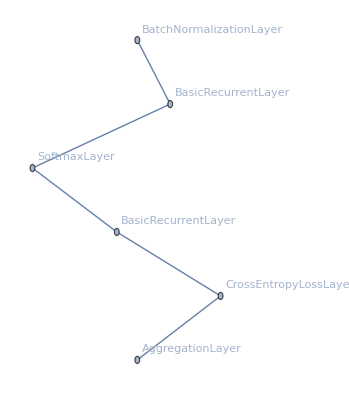

```mathematica
$nn
```